## Parsing/Dumping/Fixing/Archive

```mathematica
files={"00","01","02","03","04","05","06","07","08","09","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39","40","41","42","43","44","45","46","47","48","49","50","51","52","53","54","55","56","57","58","59","60","61","62","63","64","65","66","67","68","69","70","71","72"};
prefix="D:\\SSDWorking\\";
domains={};
Map[prefix<>#&,files];
```

```mathematica
MergeDomains[fname0_]:=Module[{fname=fname0,data},
data=Import[fname];
data=GatherBy[data,#[[2]]&];
data=Map[{#[[1]][[2]],Transpose[#][[1]]}&,data];
data
]
```

```mathematica
MergeDomainsWith[old0_,new0_]:=Module[{old=old0,new=new0},
Map[{#[[1]][[1]],Join[
#[[1]][[2]],If[Length[#]>1,#[[2]][[2]],{}]
]}&,GatherBy[Join[old,new],#[[1]]&]]
]
```

```mathematica
StatPrune[l0_]:=Module[{l=l0},
If[Length[l]>2,Drop[Drop[Sort[l],1],-1],l]
]
```

```mathematica
domains={};
For[i=1,i≤Length[files],i++,
Print[i];
domains=MergeDomainsWith[domains,MergeDomains[prefix<>files[[i]]]];
]
```

```mathematica
DumpSave["E:\\Working\\all.10.mx",domains];
```

```mathematica
Get["E:\\Working\\all.10.mx"];
(* There are some broken ones, so scrap those *)
(* We know that nothing should be below zero, and there isn't anything meaningful above 1100, so throw all that shit away *)
(*Map[Position[domains,#]&,Select[domains,Max[#[[2]]]>1100&]];*)
```

```mathematica
domains2=ParallelMap[{#[[1]],Select[#[[2]],0≤#<10000&]}&,domains];
Clear[domains]
domains=domains2;
Clear[domains2]
Length[domains]
```

```mathematica
ListLogLinearPlot[Flatten[Map[Transpose,
Map[Map[{
{#[[1]][[1]],Min[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Mean[StatPrune[Transpose[#][[2]]]]},{#[[1]][[1]],Max[StatPrune[Transpose[#][[2]]]]}
}&,GatherBy[#,#[[1]]&]]&,ImportTunnelCSV["E:\\Working\\iodine.10.dlwe.csv"]]
],1],Joined->True,PlotStyle->Thick,ImageSize->700,PlotLabel->"Iodine",AxesLabel->{"Target Throughput\n(bytes/second)","Metric"},PlotLegend->{"Client-to-Server Min","Client-to-Server Mean","Client-to-Server Max","Server-to-Client Min","Server-to-Client Mean","Server-to-Client Max"},LegendPosition->{0.4,-0.2},LegendSize->{0.6,0.3}]
```

## Analysis: Tunnels

```mathematica
ImportTunnelCSV[fname0_]:=Module[{fname=fname0,g},
g=SortBy[GatherBy[Import[fname],#[[2]]&],#[[2]]&];
Map[Map[{#[[1]],#[[3]]}&,#]&,g]
]
```

```mathematica
StatPrune[l0_]:=Module[{l=l0},
If[Length[l]>2,Drop[Drop[Sort[l],1],-1],l]
]
```

```mathematica
<<PlotLegends`
```

```mathematica
sIodine=Sort[Transpose[Flatten[ImportTunnelCSV["E:\\Working\\iodine.10.dlwe.csv"],1]][[2]]];
sDNScat=Sort[Transpose[Flatten[ImportTunnelCSV["E:\\Working\\dnscat.10.dlwe.csv"],1]][[2]]];
sDNS2TCP=Sort[Transpose[Flatten[ImportTunnelCSV["E:\\Working\\dns2tcp.10.dlwe.csv"],1]][[2]]];
sProbdns=Sort[Transpose[Flatten[ImportTunnelCSV["E:\\Working\\prob-dns.10.dlwe.csv"],1]][[2]]];
```

```mathematica
scIodine=MakeCumulative[sIodine];
scDNScat=MakeCumulative[sDNScat];
scDNS2TCP=MakeCumulative[sDNS2TCP];
scProbdns=MakeCumulative[sProbdns];
```

```mathematica
lIodine=ListInterpolation[sIodine,{{0,1}}];
lDNScat=ListInterpolation[sDNScat,{{0,1}}];
lDNS2TCP=ListInterpolation[sDNS2TCP,{{0,1}}];
lProbdns=ListInterpolation[sProbdns,{{0,1}}];
```

## Analysis : Big

```mathematica
MakeCumulative[l0_]:=Module[{l=l0,t,i,s=0},
t=Tally[l];
Reap[For[i=1,i≤Length[t],i++,
s+=t[[i]][[2]];
Sow[{t[[i]][[1]],1-s/Length[l]}];
]][[2]][[1]]
]
```

```mathematica
Get["E:\\Working\\all.10.mx"];//AbsoluteTiming
```

{4.5855818,Null}

```mathematica
sMean=Sort[ParallelMap[Mean[StatPrune[#[[2]]]]&,domains]];//AbsoluteTiming
sMedian=Sort[ParallelMap[Median[StatPrune[#[[2]]]]&,domains]];//AbsoluteTiming
sMin=Sort[ParallelMap[Min[StatPrune[#[[2]]]]&,domains]];//AbsoluteTiming
sMax=Sort[ParallelMap[Max[StatPrune[#[[2]]]]&,domains]];//AbsoluteTiming
```

{32.716158,Null}

{27.309471,Null}

{26.756406,Null}

{26.850411,Null}

```mathematica
lMean=ListInterpolation[sMean,{{0,1}}];//AbsoluteTiming
lMedian=ListInterpolation[sMedian,{{0,1}}];//AbsoluteTiming
lMin=ListInterpolation[sMin,{{0,1}}];//AbsoluteTiming
lMax=ListInterpolation[sMax,{{0,1}}];//AbsoluteTiming
```

{4.5255804,Null}

{4.506573,Null}

{4.5785819,Null}

{4.243539,Null}

```mathematica
scMean=MakeCumulative[sMean];//AbsoluteTiming
scMedian=MakeCumulative[sMedian];//AbsoluteTiming
scMin=MakeCumulative[sMin];//AbsoluteTiming
scMax=MakeCumulative[sMax];//AbsoluteTiming
```

{0.98213,Null}

{0.225034,Null}

{0.117015,Null}

{0.248032,Null}

```mathematica
ListPlot[{scMean,scMedian,scMin,scMax},Joined->True,PlotStyle->Thick]
```

-Graphics-

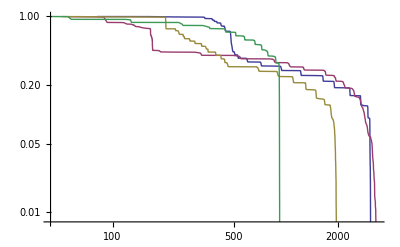

```mathematica
ListLogLogPlot[{scIodine,scDNScat,scDNS2TCP,scProbdns},Joined->True,PlotStyle->Thick,PlotRange->{{0,3000},{0,1}}]
```

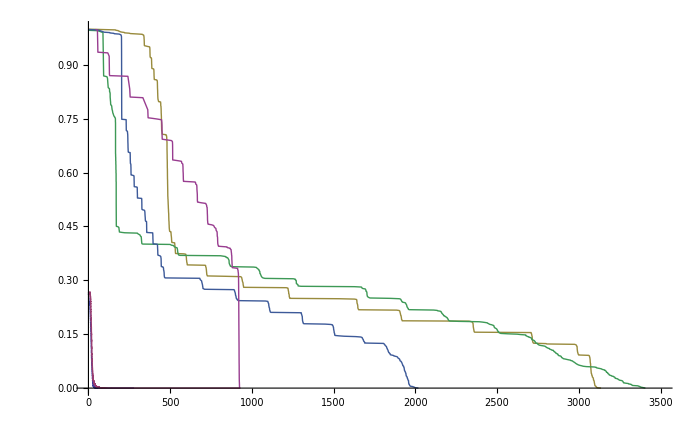

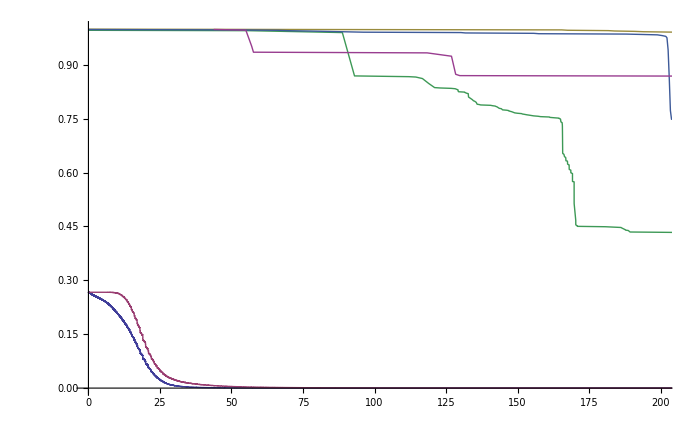

```mathematica
ListPlot[{scMean,scMax,scIodine,scDNScat,scDNS2TCP,scProbdns},Joined->True,PlotStyle->Thick,PlotRange->{{0,3500},{0,1}},PlotLegend->{"Normal Mean","Normal Max","Iodine","DNScat","DNS2TCP","DNS Probcode"},LegendPosition->{0,0},LegendSize->{0.4,0.3},ImageSize->700]
ListPlot[{scMean,scMax,scIodine,scDNScat,scDNS2TCP,scProbdns},Joined->True,PlotStyle->Thick,PlotRange->{{0,200},{0,1}},PlotLegend->{"Normal Mean","Normal Max","Iodine","DNScat","DNS2TCP","DNS Probcode"},LegendPosition->{0,0},LegendSize->{0.4,0.3},ImageSize->700]
```